```mathematica
roll:=Sort[Random[Integer,{1,6}]&/@Range[4]][[2;;]];
```

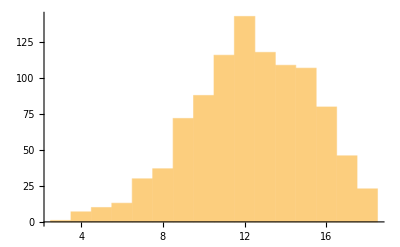

```mathematica
Histogram[Total[roll]&/@Range[1000]]
```

```mathematica
stat:=Total[roll]&/@Range[6];
```

```mathematica
stats=stat&/@Range[1000];
```

```mathematica
(values[#[[1]]]=#[[2]])&/@Transpose[{Range[3,18],{-.05,-.04,-.03,-.02,-.01,0,1,2,3,4,5,7,9,100,101,102}}]
```

{-0.05,-0.04,-0.03,-0.02,-0.01,0,1,2,3,4,5,7,9,100,101,102}

```mathematica
stats=stat&/@Range[100000];
```

27162

```mathematica
(values2[#[[1]]]=#[[2]])&/@Transpose[{Range[3,18],{-104,-103,-102,-101,-100,0,1,2,3,4,5,7,9,9.01,9.02,9.03}}]
```

{-104,-103,-102,-101,-100,0,1,2,3,4,5,7,9,9.01,9.02,9.03}

```mathematica
Length@Select[stats,Total[values/@#]<27&]
Length@Select[stats,Total[values2/@#]>27&]
Length@Select[stats,Total[values2/@#]==27&]
100000-%-%%-%%%
```

27438

46508

1776

24278

```mathematica
1/(1-(1-1/6^4.)^24)
```

54.4807

```mathematica
6^3
```

216

```mathematica
Mean[Total[values5/@#]&/@stats]//N
```

28.3688

```mathematica
(values3[#[[1]]]=#[[2]])&/@Transpose[{Range[3,18],{-5,-4,-3,-2,-1,0,1,2,3,4,5,7,9,11,13,15}}]
```

{-5,-4,-3,-2,-1,0,1,2,3,4,5,7,9,11,13,15}

```mathematica
(values4[#[[1]]]=#[[2]])&/@Transpose[{Range[3,18],{-10,-8,-6,-4,-2,0,1,2,3,4,5,7,9,10,11,12}}]
```

{-10,-8,-6,-4,-2,0,1,2,3,4,5,7,9,10,11,12}

```mathematica
(values5[#[[1]]]=#[[2]])&/@Transpose[{Range[3,18],{0,0,0,0,0,0,1,2,3,4,5,7,9,9,9,9}}]
```

{0,0,0,0,0,0,1,2,3,4,5,7,9,9,9,9}

```mathematica
Total[values/@{17,16,13,13,12,7}]
```

```mathematica
15*4.5
```

67.5

```mathematica
100/15.
```

6.66667

```mathematica
1/CDF[NormalDistribution[],-4.5]
```

294319.

```mathematica
6^24
```

4738381338321616896

```mathematica
s
```

```mathematica
Round[100*(6^4/21)^6]
```

5524770484049

```mathematica
Tally@Flatten@Table[Total[Sort[{a,b,c,d}][[2;;]]],{a,1,6},{b,1,6},{c,1,6},{d,1,6}]
```

{{3,1},{4,4},{5,10},{6,21},{7,38},{8,62},{9,91},{10,122},{11,148},{12,167},{13,172},{14,160},{15,131},{16,94},{17,54},{18,21}}

```mathematica
{#[[1]],#[[2]]/6^4}&/@%
```

{{3,1/1296},{4,1/324},{5,5/648},{6,7/432},{7,19/648},{8,31/648},{9,91/1296},{10,61/648},{11,37/324},{12,167/1296},{13,43/324},{14,10/81},{15,131/1296},{16,47/648},{17,1/24},{18,7/432}}

```mathematica
%//N
```

{{3.,0.000771605},{4.,0.00308642},{5.,0.00771605},{6.,0.0162037},{7.,0.029321},{8.,0.0478395},{9.,0.070216},{10.,0.0941358},{11.,0.114198},{12.,0.128858},{13.,0.132716},{14.,0.123457},{15.,0.10108},{16.,0.0725309},{17.,0.0416667},{18.,0.0162037}}

```mathematica
%[[All,2]]
```

{0.000771605,0.00308642,0.00771605,0.0162037,0.029321,0.0478395,0.070216,0.0941358,0.114198,0.128858,0.132716,0.123457,0.10108,0.0725309,0.0416667,0.0162037}

```mathematica
Accumulate@%
```

{0.000771605,0.00385802,0.0115741,0.0277778,0.0570988,0.104938,0.175154,0.26929,0.383488,0.512346,0.645062,0.768519,0.869599,0.94213,0.983796,1.}

```mathematica
(1-0.10493827160493827)^(6*Range[12])
```

{0.514183,0.264384,0.135942,0.0698991,0.035941,0.0184802,0.00950223,0.00488589,0.00251224,0.00129175,0.000664197,0.000341519}